```mathematica
hvec = {10^0,10^-1,10^-2,10^-3,1*^-4,1*^-5,1*^-6,1*^-7,1*^-8,1*^-9,1*^-10,1*^-11,1*^-12,1*^-13}
```

{1,1/10,1/100,1/1000,1/10000,1/100000,1/1000000,1/10000000,1/100000000,1/1000000000,1/10000000000,1/100000000000,1/1000000000000,1/10000000000000}

```mathematica
c = -100
```

-100

```mathematica
Fval =N[(Exp[c*hvec]-1)/c ,15]
```

{0.01,0.00999954600070238,0.00632120558828558,0.000951625819640404,0.0000995016625083195,9.99500166625008×10^-6,9.99950001666625×10^-7,9.99995000016667×10^-8,9.99999500000167×10^-9,9.99999950000002×10^-10,9.99999995×10^-11,9.999999995×10^-12,9.9999999995×10^-13,9.99999999995×10^-14}

```mathematica
bval = N[(Exp[c*hvec]-(1+c*hvec))/(c^2*hvec),16]
```

{0.0099,0.009000045399929762,0.003678794411714423,0.0004837418035959573,0.00004983374916805357,4.998333749916681×10^-6,4.999833337499917×10^-7,4.999983333375×10^-8,4.99999833333375×10^-9,4.999999833333337×10^-10,4.999999983333333×10^-11,4.999999998333333×10^-12,4.999999999833333×10^-13,4.999999999983333×10^-14}

```mathematica
}
```

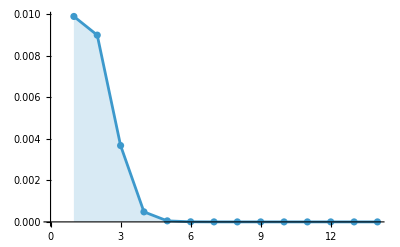

```mathematica
ListPlot[bval,Filling->Axis,Mesh->All,Joined->True]
```

```mathematica
N[%34]
```

{1.71828,1.05171,1.00502,1.0005,1.00005,1.00001,1.,1.,1.,1.,1.,1.,1.00009,0.999201}

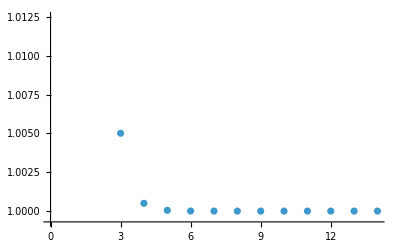

```mathematica
ListPlot[%34]
```

```mathematica
diff = N[(Exp[c*hvec]-1)/c - (Exp[c*hvec]-(1+c*hvec))/(c^2*hvec),16]
```

{0.0001,0.0009995006007726127,0.002642411176571154,0.000467884016044447,0.00004966791334026589,4.996667916333403×10^-6,4.999666679166333×10^-7,4.999966666791666×10^-8,4.999996666667917×10^-9,4.999999666666679×10^-10,4.999999966666667×10^-11,4.999999996666667×10^-12,4.999999999666667×10^-13,4.999999999966667×10^-14}